```mathematica
μE=9.284*10^-24;
R=100*10^-12;
μ0=4π * 10^-7;
eV=1.602*10^-19;
eVtoKy=8065.73;
(μ0/(4 π)* μE^2/R^3)1/eV*eVtoKy
```

0.433962

```mathematica
(μ0/(4 π)* μE^2/R^3)1/eV*10^6
```

53.8032

```mathematica
PositionIndex[{1,1,2}]
```

<|1→{1,2},2→{3}|>

```mathematica
zeroIndices
```

{}

```mathematica
allIndices
```

{1,2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
nonZeroIndices
```

{2,3,4,5,6,7,8,9,10,11,12}

```mathematica
hLabels
```

{{2,Pr},{3,Nd},{4,Pm},{5,Sm},{6,Eu},{7,Gd},{8,Tb},{9,Dy},{10,Ho},{11,Er},{12,Tm}}

```mathematica
values
```

{68878.,73018.,76400.,79805.,83125.,85669.,88995.,91903.,94564.,97483.,100134.}

```mathematica
hLabels
```

{{3,Nd}^(3+),{4,Pm}^(3+),{5,Sm}^(3+),{6,Eu}^(3+),{7,Gd}^(3+),{8,Tb}^(3+),{9,Dy}^(3+),{10,Ho}^(3+),{11,Er}^(3+),{12,Tm}^(3+)}

```mathematica
keyParams={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B22,B24,B44,B26,B46,B66};
carnallVal=Transpose[Values[(keyParams/.#)&/@Carnall["data"]]];
allIndices=Range[13];
horizonLabels=Transpose[{allIndices,StringSplit["Ce Pr Nd Pm Sm Eu Gd Tb Dy Ho Er Tm Yb"," "]}];
paramPlots=Table[(
values=carnallVal[[i]];
values=Transpose[{allIndices,values}];
zeroIndices=Flatten[Position[values,0.]];
nonZeroIndices=Complement[allIndices,zeroIndices];
values=values[[nonZeroIndices]];
hLabels=horizonLabels[[nonZeroIndices]];
hLabels={#[[1]],Superscript[#[[2]],"3+"]}&/@hLabels;
ListPlot[values,
PlotLabel->Style[keyParams[[i]],20],
ImageSize->800,
AspectRatio->1/2,
Frame->True,
FrameStyle->Directive[15],
FrameLabel->{"",ToString[keyParams[[i]]]<>" / Ky"},
FrameTicks->{{Automatic,All},{hLabels,hLabels}}
]),{i,1,Length[carnallVal]}];
```

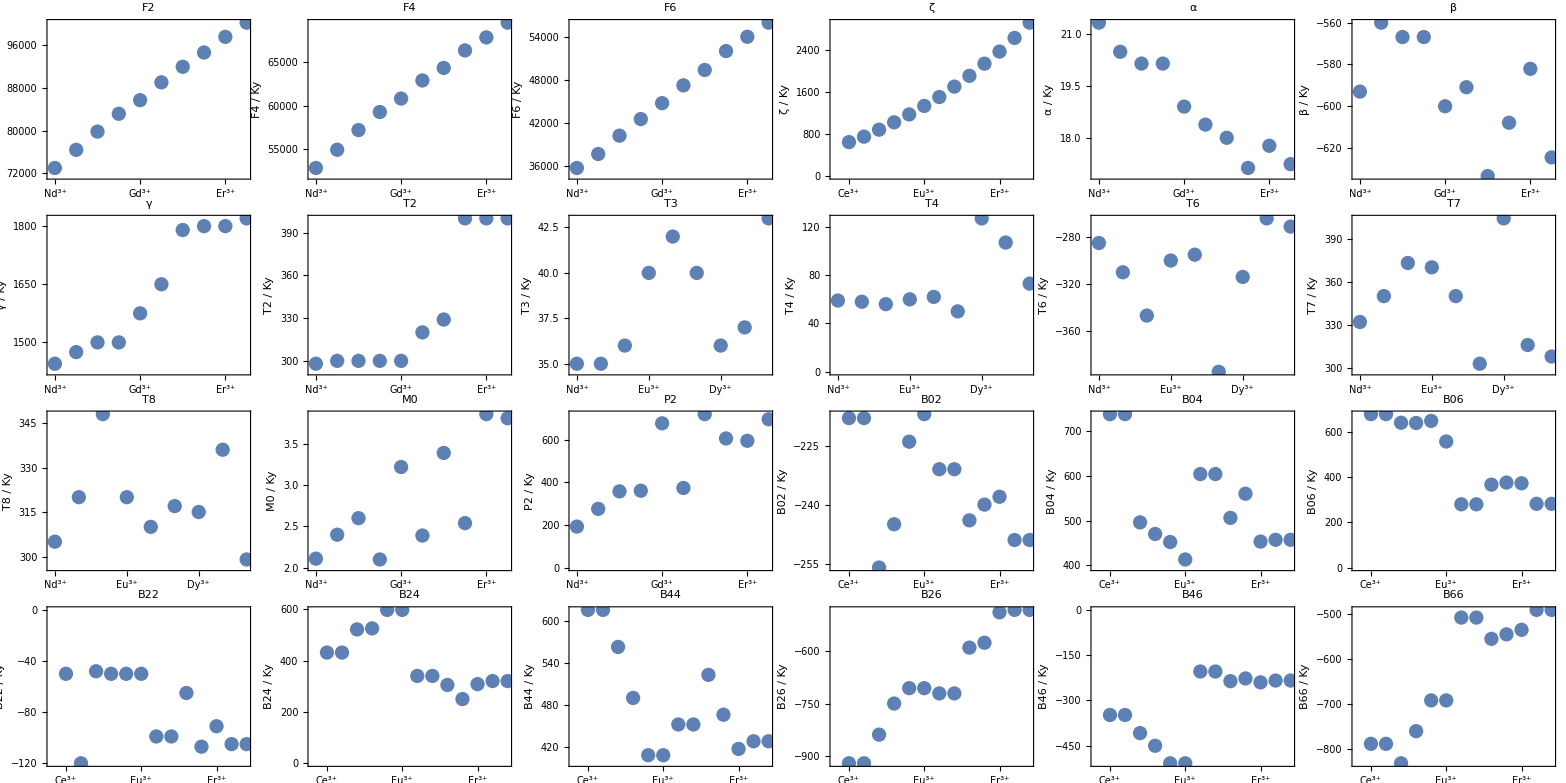

```mathematica
superLanthanum=Grid[Partition[paramPlots,6]]
```

```mathematica
Export["~/Desktop/LaF3.pdf",superLanthanum]
```

~/Desktop/LaF3.pdf